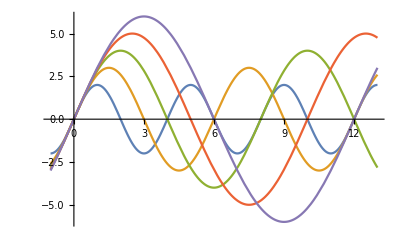

```mathematica
Plot[{2Sin[(x*Pi)/2],3Sin[(x*Pi)/3], 4Sin[(x*Pi)/4], 5Sin[(x*Pi)/5], 6Sin[(x*Pi)/6]}, {x,-1, 13}]
```

```mathematica
Plot[Product[Sin[(x*pi)/n], {n,2, Infinity}]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[∏_(n=2)^∞ Sin[(x pi)/n]]

```mathematica
Product[Sin[(x/n)*Pi], {n,2, 10}]
```

Sin[(π x)/10] Sin[(π x)/9] Sin[(π x)/8] Sin[(π x)/7] Sin[(π x)/6] Sin[(π x)/5] Sin[(π x)/4] Sin[(π x)/3] Sin[(π x)/2]

```mathematica
Plot[Product[Sin[(x*pi)/n], {n,2, Infinity}], {x, -1, 13}]
```

NProduct::nplim: Limit of product n is not a number.

General::stop: Further output of NProduct::nplim will be suppressed during this calculation.

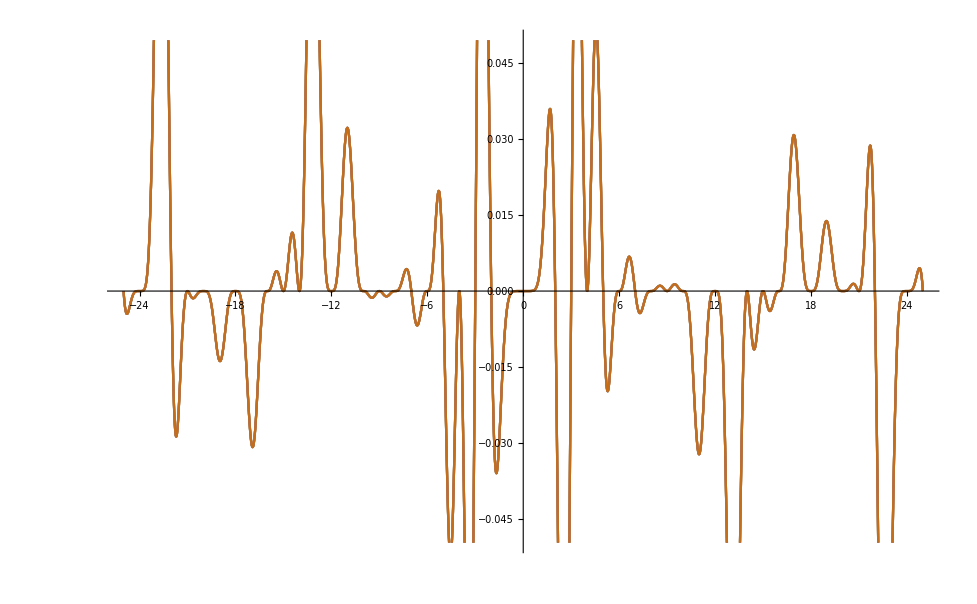

```mathematica
f[x_,t_,nm_]:=Product[Sin[(x*Pi)/n],{n,2,nm}];
Plot[Table[f[x,t,10],{t,{0,0.01,0.1,0.5,1,20}}]//Evaluate,{x,-25,25}]
```